# Plot C++ output Sim2

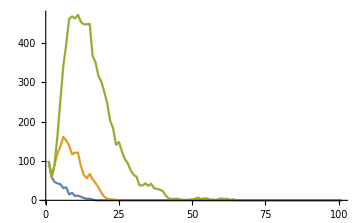

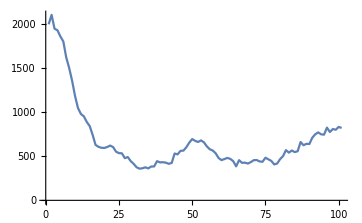

```mathematica
data=Import["C:\\Users\\Freek\\Documents\\GeneDrive\\Data\\sim_results.csv"][[2;;,;;]];
drive1={2,4,6,8};
drive2={3,4,7,8};
drive3={5,6,7,8};
wildtype={1,2,3,4};
ListLinePlot[{Total[data[[;;,locus1]],{2}],Total[data[[;;,locus2]],{2}],Total[data[[;;,locus3]],{2}]},PlotRange->All]
ListLinePlot[Total[data[[;;,wildtype]],{2}],PlotRange->All]
```